```mathematica
ClearAll["Global`*"]
```

# Example Plotting Script for the Gershgorin-Harlim-Majda 2010 System

## Import Data

```mathematica
hereDir = NotebookDirectory[];
dataDir = FileNameJoin[{hereDir,"..","build"}];
runCount = 250;
importNetCDFArg = {"Datasets",Table[StringJoin["run",StringPadLeft[ToString[i],8,"0"]],{i,1,runCount}]};
rawData = Import[FileNameJoin[{dataDir,"out.nc"}],importNetCDFArg];
```

## Single-Run Plot

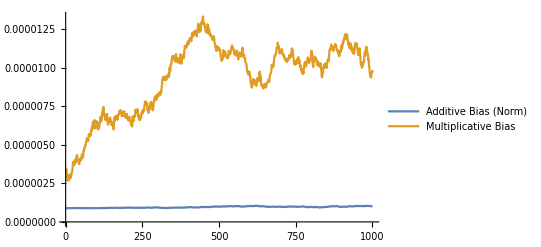

```mathematica
runNum =104;
timeStepNum = rawData[[runNum]][[;;,1]];
time=rawData[[runNum]][[;;,2]];
addBias = rawData[[runNum]][[;;,3]] + ⅈ rawData[[runNum]][[;;,4]];
multBias = rawData[[runNum]][[;;,5]];
stateVar = rawData[[runNum]][[;;,6]] + ⅈ rawData[[runNum]][[;;,7]];

ListLinePlot[{Abs[addBias],multBias},PlotRange->All,PlotLegends->{"Additive Bias (Norm)", "Multiplicative Bias", "State Variable (Norm)"}]
```

## Analytic Equations

```mathematica
meanBAnal[t_]:= meanB + (meanB0 - meanB)ⅇ^(lambdaB (t - t0))
varBAnal[t_]:=varB0 ⅇ^(-2 dampB (t - t0))+noiseStrB^2/(2 dampB)(1 - ⅇ^(-2 dampB (t - t0)))
covBConjgBAnal[t_]:=covB0ConjgB0 ⅇ^(2 lambdaB (t - t0))
meanGammaAnal[t_]:=meanGamma + (meanGamma0 - meanGamma)ⅇ^(-dampGamma(t - t0))
varGammaAnal[t_]:=varGamma0 ⅇ^(-2 dampGamma (t - t0))+noiseStrGamma^2/(2 dampGamma)(1 - ⅇ^(-2 dampGamma (t - t0)))
```

## Multi-Run Mean Plot

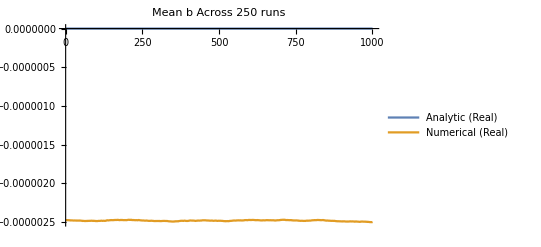

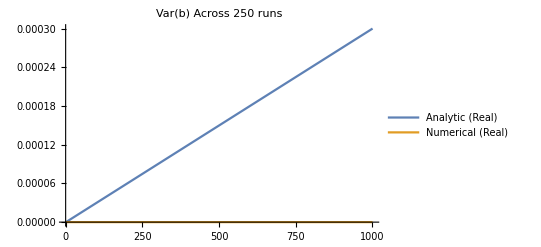

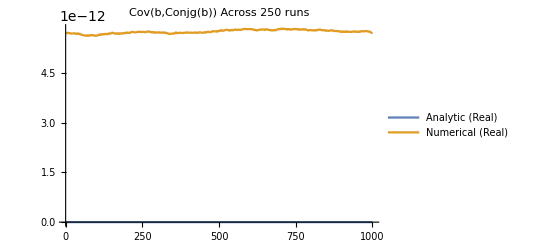

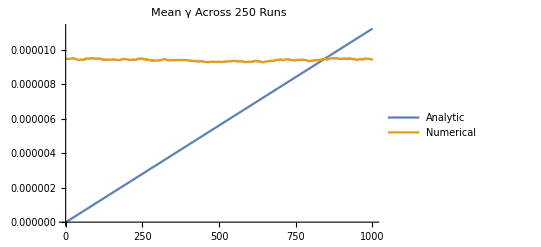

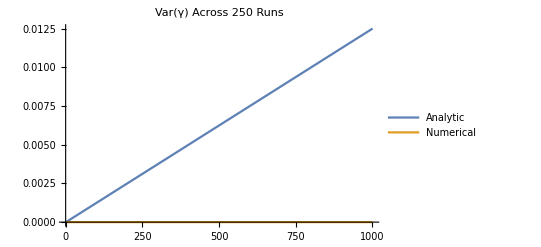

```mathematica
t0 = time[[1]];
Δt = time[[2]]-time[[1]];
meanB = 0.0+ⅈ 0.0;
meanB0 = 0.0 + ⅈ 0.0;
dampB = 0.15;
oscFreqB = 1.78;
lambdaB = -dampB + ⅈ oscFreqB;
noiseStrB = 0.7745;
varB0 = 0.0;
covB0ConjgB0 = 0.0;


meanGamma = 1.5;
meanGamma0 = 0.0;
dampGamma = 0.015;
noiseStrGamma = 5.0;
varGamma0 = 0.0;


meanAddBias=Mean[rawData[[;;,;;,3]] + ⅈ rawData[[;;,;;,4]]];
meanMultBias = Mean[rawData[[;;,;;,5]]];
meanStateVar = Mean[rawData[[;;,;;,6]] + ⅈ rawData[[;;,;;,7]]];

varAddBias =Table[Covariance[rawData[[;;,i,3]] + ⅈ rawData[[;;,i,4]],rawData[[;;,i,3]] + ⅈ rawData[[;;,i,4]]],{i,1,Length[time],1}];
covAddBiasConjgAddBias = Table[Covariance[rawData[[;;,i,3]] + ⅈ rawData[[;;,i,4]],rawData[[;;,i,3]] - ⅈ rawData[[;;,i,4]]],{i,1,Length[time],1}];

varMultBias = Table[Covariance[rawData[[;;,i,5]],rawData[[;;,i,5]]],{i,1,Length[time],1}];


ListLinePlot[{Table[Re[meanBAnal[t0 + i * Δt]],{i,0,Length[time]-1}],Re[meanAddBias]},PlotLegends->{"Analytic (Real)","Numerical (Real)"},PlotLabel->"Mean b Across 250 runs"]
ListLinePlot[{Table[Re[varBAnal[t0 + i * Δt]],{i,0,Length[time]-1}],Re[varAddBias]},PlotLegends->{"Analytic (Real)","Numerical (Real)"},PlotLabel->"Var(b) Across 250 runs"]
ListLinePlot[{Table[Re[covBConjgBAnal[t0 + i * Δt]],{i,0,Length[time]-1}],Re[covAddBiasConjgAddBias]},PlotLegends->{"Analytic (Real)","Numerical (Real)"},PlotLabel->"Cov(b,Conjg(b)) Across 250 runs"]
ListLinePlot[{Table[meanGammaAnal[t0 + i * Δt],{i,0,Length[time]-1}],meanMultBias},PlotLegends->{"Analytic","Numerical"}, PlotRange->All, PlotLabel->"Mean γ Across 250 Runs"]
ListLinePlot[{Table[varGammaAnal[t0 + i * Δt],{i,0,Length[time]-1}],varMultBias},PlotLegends->{"Analytic","Numerical"}, PlotRange->All, PlotLabel->"Var(γ) Across 250 Runs"]
```